# Efficient Water - Cooled Bitter - Type Electromagnet for Zeeman Slowing in Cold - Atom Experiments

## Rishav Koirala and Ben A. Olsen 2025

## Thermal Measurements

The FLIR thermal imaging camera produces .jpg files (in the thermal_data folder), and FLIR provides a software suite that can convert them to .csv files (https://www.flir.com/products/flir-thermal-studio-suite/?srsltid=AfmBOopCQmWCasnifR4ixrOgVXhfD0eWfw7VyX34fKqQ636rIWE7J8uU). While this is paid software, they seem to offer a free trial period. We suspect the images could be similarly analyzed using a python image analysis script.

Import all the csv files produced for thermal images taken at various times since turning on the 200-A current in the coil.

```mathematica
filetlt0=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=0-.csv"],"Data"];
filet0=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=0.csv"],"Data"];
filet4=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=4.csv"],"Data"];
filet7=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=7.csv"],"Data"];
filet11=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=11.csv"],"Data"];
filet14=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=14.csv"],"Data"];
filet18=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=18.csv"],"Data"];
filet21=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=21.csv"],"Data"];
filet25=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=25.csv"],"Data"];
filet29=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=29.csv"],"Data"];
filet32=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=32.csv"],"Data"];
filet36=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=36.csv"],"Data"];
filet40=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=40.csv"],"Data"];
filet43=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=43.csv"],"Data"];
filet47=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=47.csv"],"Data"];
filet50=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=50.csv"],"Data"];
filet54=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=54.csv"],"Data"];
filet57=Import[StringJoin[NotebookDirectory[],"/thermal_data/t=57.csv"],"Data"];
```

```mathematica
datatlt0 = Table[{filetlt0[[jj]][[1]],filetlt0[[jj]][[2]]}, {jj, 2, Length[filetlt0]-1}];
datat0 = Table[{filetlt0[[jj]][[1]],filet0[[jj]][[2]]}, {jj, 2, Length[filet0]}];
datat4 = Table[{filetlt0[[jj]][[1]],filet4[[jj]][[2]]}, {jj, 2, Length[filet4]}];
datat7 = Table[{filetlt0[[jj]][[1]],filet7[[jj]][[2]]}, {jj, 2, Length[filet7]}];
datat11 = Table[{filetlt0[[jj]][[1]],filet11[[jj]][[2]]}, {jj, 2, Length[filet11]}];
datat14 = Table[{filetlt0[[jj]][[1]],filet14[[jj]][[2]]}, {jj, 2, Length[filet14]}];
datat18 = Table[{filetlt0[[jj]][[1]],filet18[[jj]][[2]]}, {jj, 2, Length[filet18]}];
datat21 = Table[{filetlt0[[jj]][[1]],filet21[[jj]][[2]]}, {jj, 2, Length[filet21]}];
datat25 = Table[{filetlt0[[jj]][[1]],filet25[[jj]][[2]]}, {jj, 2, Length[filet25]}];
datat29 = Table[{filetlt0[[jj]][[1]],filet29[[jj]][[2]]}, {jj, 2, Length[filet29]}];
datat32 = Table[{filetlt0[[jj]][[1]],filet32[[jj]][[2]]}, {jj, 2, Length[filet32]}];
datat36 = Table[{filetlt0[[jj]][[1]],filet36[[jj]][[2]]}, {jj, 2, Length[filet36]}];
datat40 = Table[{filetlt0[[jj]][[1]],filet40[[jj]][[2]]}, {jj, 2, Length[filet40]}];
datat43 = Table[{filetlt0[[jj]][[1]],filet43[[jj]][[2]]}, {jj, 2, Length[filet43]}];
datat47 = Table[{filetlt0[[jj]][[1]],filet47[[jj]][[2]]}, {jj, 2, Length[filet47]}];
datat50 = Table[{filetlt0[[jj]][[1]],filet50[[jj]][[2]]}, {jj, 2, Length[filet50]}];
datat54 = Table[{filetlt0[[jj]][[1]],filet54[[jj]][[2]]}, {jj, 2, Length[filet54]}];
datat57 = Table[{filetlt0[[jj]][[1]],filet57[[jj]][[2]]}, {jj, 2, Length[filet57]}];

Alldata = {datatlt0, datat0, datat4,datat7,datat11,datat14,datat18,datat21,datat25,datat29,datat32,datat36,datat40,datat43,datat47,datat50, datat54, datat57};

times = {-1, 0, 4, 7, 11, 14, 18, 21, 25, 29, 32, 36, 40, 43, 47, 50, 54, 57};
uncert = 0.2;
chilledWaterTemp = 20;

datat36mod = Table[{filetlt0[[jj]][[1]],Around[filet36[[jj]][[2]], uncert]-chilledWaterTemp}, {jj, 2, Length[filet36]}];
```

Define the three points for plotting a timeseries

{{-1,0.520.20},{0,1.380.20},{4,14.490.20},{7,19.490.20},{11,22.220.20},{14,23.190.20},{18,23.840.20},{21,23.530.20},{25,24.470.20},{29,23.970.20},{32,24.270.20},{36,24.330.20},{40,23.900.20},{43,23.800.20},{47,24.000.20},{50,23.900.20},{54,23.680.20},{57,24.090.20}}

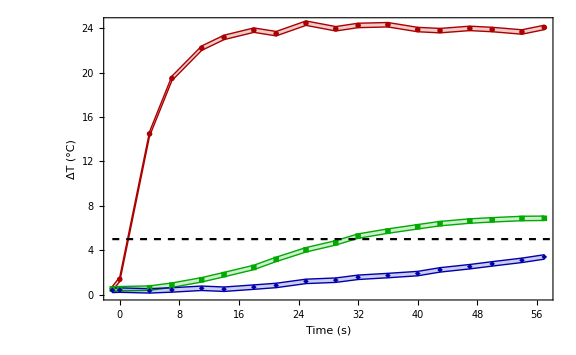

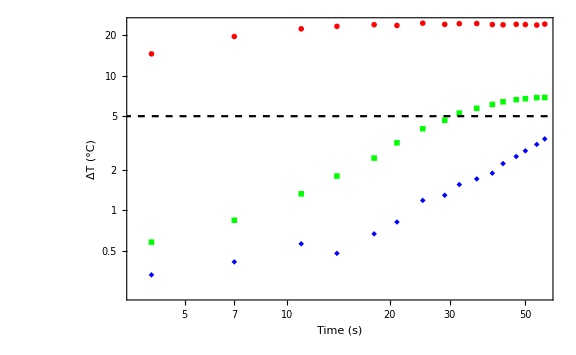

```mathematica
OvenSide = Table[{times[[ii]], Around[Alldata[[ii]][[5]][[2]], uncert]-chilledWaterTemp}, {ii, Length[times]}] (* pixel 5 *)
Middle = Table[{times[[ii]], Around[Alldata[[ii]][[132]][[2]], uncert]-chilledWaterTemp}, {ii, Length[times]}]; (* pixel 132 *)
MOTSide = Table[{times[[ii]], Around[Alldata[[ii]][[260]][[2]], uncert]-chilledWaterTemp}, {ii, Length[times]}]; (* pixel 260 *)

Show[ListPlot[{OvenSide, Middle, MOTSide}, Frame->True, PlotStyle->{Darker[Red], Darker[Green], Darker[Blue]}, Joined->False, IntervalMarkers->"Bands", Mesh->All, FrameLabel->{Style["Time (s)", 25, Black], Style[Rotate["ΔT (°C)", Degree 0], 25, Black]}, FrameTicksStyle->Directive[Black,25], FrameStyle->Thick, PlotMarkers->{{Automatic, 0.04}}, ImageSize->Large],
Plot[5., {t, -1,60}, PlotStyle->{Black, Dashed}], BaseStyle->{FontFamily->"Times",FontSize->25}]
Show[ListLogLogPlot[{OvenSide, Middle, MOTSide}, Frame->True, PlotStyle->{Red, Green, Blue}, Joined->False, IntervalMarkers->"Bands", IntervalMarkersStyle-> {Pink, LightGreen, LightBlue}, Mesh->All, FrameLabel->{Style["Time (s)", 18, Black], Style[Rotate["ΔT (°C)", Degree 0], 25, Black]}, FrameTicksStyle->Directive[Black,18], FrameStyle->Thick,PlotMarkers->{{Automatic, 0.04}},BaseStyle->{FontFamily->"Times",FontSize->25}],
Plot[Log[5.], {t, -1,60}, PlotStyle->{Black, Dashed}]]
```

Plot the spatial temperature distribution at an intermediate time

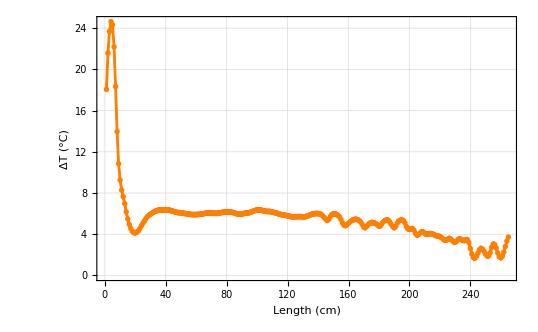

```mathematica
ListPlot[datat36mod, Frame->True, PlotStyle->Orange, Joined->True, IntervalMarkers->"Bands", IntervalMarkersStyle-> Red, Mesh->All, PlotRange->All,FrameLabel->{Style["Length (cm)", 18, Black], Style["ΔT (°C)", 18, Black]}, FrameTicksStyle->Directive[Black,18], FrameStyle->Thick]
```